# I Convolution

KTH/EECS:IX1501 - Mathematical Statistics
HT 2018

## Section. Implementation and Assessment

The course includes three project tasks on a total of 4 hp. The projects are assessed in writing and orally. They will be given a summary grade in scale A-F. The assessment includes the number of solved project tasks and the quality. 

The first two projects are mandatory. Each project is divided into basic and advanced tasks. Solving only basic tasks in the two projects will lead to E. Solving advanced tasks provides a chance to increase the grade to D or C. The third project is optional, and targets higher grades. Solving tasks of the third project will improve your grade up to two steps.

In project 1 and 2,  you will work in a group of two and solve a mathematical task, write a report (Swedish or English) in Mathematica and prepare a short oral presentation on your solution to the task (Swedish or English).

Carefully read the following information so that you know which rules apply and what is expected from you.

### Section.Subsection Report

The report should be written in Mathematica and contain

title and authors of the report

email@kth.se

a summary containing the results of resolved parts

separate sections for each part containing e.g.

mathematical formulas and equations

a brief discussion

explanatory diagrams

your conclusions.

separate code section (do not mix code and text with conclusions and results)

The report will normally be uploaded a couple of days prior to the examination (see 1.4 below).

### Section.Subsection Oral Presentation

You should prepare an oral presentation of your solution to the task. The presentation will be carried out with your own laptop and should not take more than five minutes, effective time. A projector will be available at the presentation. Please carefully consider your presentation, what is important, in what order and how it will be illustrated. Practice the presentation in advance and make sure to meet the time frame. One of you in the group (of two) will be selected randomly for the oral presentation and the other will be selected for questioning.

### Section.Subsection Rules

The task is considered individually and assumes that you have full knowledge of all the material you are presenting. In order to be approved, you must have solved the task and be able to explain the entire task and solution.

To account for the task that you do not have solved is considered cheating. It is also cheating to copy the whole or a part of a solution from others. If two solutions are deemed as (partial) copies, they are rejected both.

If the solution contains parts that you do not have produced, e.g. background material, you must clearly indicate this and specify the source.

Suspicion of cheating or misleading can be reported to the Disciplinary Board.

### Section.Subsection Examination

The examination is carried out according to the booking in Canvas.

The booking is done according to information at KTH Canvas Projektuppgifter/Projekt 1.

Please notice that this project should be reported in group of two students.

The report (including code section) should be uploaded according to the information in Canvas Projektuppgifter/Projekt 1.

A printed copy of the report must be submitted at examination. Don’t print the code section.

Notice that the report shall always be uploaded in time even if you cannot attend at the oral presentation. In case of illness, etc., then the oral presentation may be made during project 3. If you are unable to attend, you must in advance inform the teachers, Haris Celik (harisc@kth.se) and Ki Won Sung (sungkw@kth.se), in writing.

If you ignore the oral presentation or the uploading of the report without contacting the teachers (in writing), you will have to wait for the next course for a new project exam.

## Section. Preparations

### Section.Subsection Study

Read and study the following texts:

Chapter 3-6

lecture notes F3-F6

### Section.Subsection Guidance

#### Section.Subsection.Subsubsection Language Tip

In Mathematica 11, by default, you get automatic spell-checking in English. This can be a bit annoying if you write a report in Swedish. In order to set the language to Swedish or to turn off the spell-checking, execute one of the following commands in your notebook. Then, delete the code and save your notebook.

SetOptions[EvaluationNotebook[], DefaultNaturalLanguage -> "Swedish"]

SetOptions[EvaluationNotebook[], ShowAutoSpellCheck -> False]

The spell checking, on notebook level, works on Mathematica 11.0.1 and 11.2 or later. When a word is marked as misspelled, e.g. atomatic. You can right-click the word and get a what-to-do menu. Use the second syntax above to inactivate spell-checking.

#### Section.Subsection.Subsubsection PDF, CDF in Mathematica

##### Section.Subsection.Subsubsection.Subsubsubsection Discrete rvs

A discrete probability function can be introduced by Piecewise. Example

```mathematica
ClearAll["`*"]
```

```mathematica
pfX[k_]:=Piecewise[{
{1/3, k==3},
{1/4,k==4},
{1/5,k==6},
{1-(1/3+1/4+1/5),k==11}
},
0  (* default *)
]
```

```mathematica
DiscretePlot[pfX[k],{k,0,12},AxesLabel->Automatic]
```

```mathematica
Sum[pfX[k],{k,3,11}]
```

```mathematica
μ=Sum[k pfX[k],{k,3,11}]
```

```mathematica
σ=√(Sum[k^2 pfX[k],{k,3,11}]-μ^2)
```

```mathematica
cdfX[x_]:=With[{n=Floor[x]},Sum[pfX[k],{k,1,n}]]
```

```mathematica
Plot[cdfX[x],{x,0,12},AxesLabel->Automatic]
```

It is possible to define a discrete Mathematica distribution so that built-in methods can be used:

```mathematica
Δk=1;
𝒟=ProbabilityDistribution[pfX[k],{k,3,11,Δk}];
```

```mathematica
Mean[𝒟]
```

```mathematica
StandardDeviation[𝒟]
```

```mathematica
Plot[CDF[𝒟,x],{x,0,12},AxesLabel->Automatic]
```

We can also generate random numbers from this distribution.

```mathematica
RandomVariate[𝒟]
```

```mathematica
RandomVariate[𝒟,25]
```

Notice that a simple dice can be introduced using an interval.

```mathematica
pfY[k_]:=Piecewise[{{1/6,1≤k≤6}}]
```

```mathematica
pfY/@{2,8,4.7}
```

Sometimes simplicity in programming is more important than a perfect code. As a user you decide how to use the method. In this case the method is designed for integer input, but nothing stops you to input a floating point number and get a erroneous result. However, this might not be of importance to solve your problem.

If uniqueness is important in the pattern matching, you might use the following code.

```mathematica
pfZ[k_Integer]:=Piecewise[{{1/6,1≤k≤6}}];
pfZ[k_]:=0
```

```mathematica
pfZ/@{2,8,4.7}
```

##### Section.Subsection.Subsubsection.Subsubsubsection Continuous rvs

Here’s an example of a continuous distribution. We want to define a pdf(x)∝x (1-x/5)e^-x in the interval 0<x<5. The first step is to determine the proportionality constant according to Kolmogorov’s 2^nd axiom.

```mathematica
ClearAll["`*"]
```

```mathematica
K2=Integrate[c x (1-x/5) ⅇ^-x,{x,0,5},Assumptions->c>0]==1
```

```mathematica
{c}=c/.Solve[K2,c]
```

```mathematica
N[c]
```

```mathematica
pdf[x_]=Piecewise[{{c x (1-x/5) ⅇ^-x,0<x<5}}]
```

```mathematica
Plot[pdf[x],{x,-1,6},PlotStyle->Thick,AxesLabel->Automatic]
```

```mathematica
μ=Integrate[x pdf[x],{x,0,5}]
```

```mathematica
σ=√(Integrate[x^2 pdf[x],{x,0,5}]-μ^2)//Simplify
```

```mathematica
{μ,σ}//N
```

```mathematica
cdf[x_]=Piecewise[{
{Integrate[pdf[t],{t,0,x},Assumptions->{0<x<5}],0<x<5},
{1,x≥5}
},0]
```

```mathematica
Plot[cdf[x],{x,-1,6},PlotStyle->Thick,AxesLabel->Automatic]
```

We can solve for the median with

```mathematica
{m}=m/.Solve[cdf[m]==1/2,m]
```

```mathematica
cdf[m]//FullSimplify
```

or we can use numerical methods

```mathematica
Clear[m];
m=m/.FindRoot[cdf[m]==1/2,{m,1.5}]
```

```mathematica
cdf[m]
```

As in the discrete case it is possible to define a Mathematica distribution so that built-in methods can be used:

```mathematica
𝒟=ProbabilityDistribution[pdf[x],{x,0,5}];
```

```mathematica
Mean[𝒟]
```

```mathematica
StandardDeviation[𝒟]
```

```mathematica
Plot[Evaluate[CDF[𝒟,x]],{x,-1,6},PlotStyle->Thick,AxesLabel->Automatic]
```

```mathematica
Median[𝒟]
```

```mathematica
q95=Quantile[𝒟,0.95]
```

```mathematica
CDF[𝒟,q95]
```

We can also generate random numbers from this distribution.

```mathematica
RandomVariate[𝒟]
```

```mathematica
RandomVariate[𝒟,25]
```

##### Section.Subsection.Subsubsection.Subsubsubsection Built-in distributions

In Mathematica there are around 150 built-in distributions, which can be used with standard methods like

PDF, CDF, Mean, Variance, StandardDeviation, Probability, NProbability, Median, ...

See Probability & Statistics, Discrete Distributions and Continuous Distributions.

Here’s couple of examples

Poisson distribution

```mathematica
ClearAll["`*"]
```

```mathematica
μ=3.5;
𝒟=PoissonDistribution[μ];
```

```mathematica
Mean[𝒟]
```

```mathematica
Variance[𝒟]
```

```mathematica
StandardDeviation[𝒟]
```

```mathematica
CDF[𝒟,5]
```

```mathematica
Probability[X≤5,X\[Distributed]𝒟]
```

```mathematica
Probability[X<5,X\[Distributed]𝒟]
```

Normal distribution

```mathematica
ClearAll["`*"]
```

```mathematica
(* standard cdf *)
Φ[x_]:=Evaluate[CDF[NormalDistribution[0,1],x]]
```

```mathematica
μ=4.75;
σ=1.5;
𝒟=NormalDistribution[μ,σ];
```

```mathematica
CDF[𝒟,5]
```

```mathematica
Probability[X≤5,X\[Distributed]𝒟]
```

```mathematica
Probability[X<5,X\[Distributed]𝒟]
```

```mathematica
Φ[(5-μ)/σ]
```

```mathematica
Plot[PDF[𝒟,x],{x,-2,12},AxesLabel->Automatic]
```

```mathematica
Plot[CDF[𝒟,x],{x,-2,12},AxesLabel->Automatic]
```

```mathematica
Plot[Φ[(x-μ)/σ],{x,-2,12},AxesLabel->Automatic]
```

#### Section.Subsection.Subsubsection Convolution

##### Section.Subsection.Subsubsection.Subsubsubsection Discrete convolution

The distribution of a sum of two independent discrete random variables (rvs) S=X+Y can be determined by the following reasoning. If the sum S=s and we have X=i then Y=s-i. Since  X and  Y are independent the probability is

P(X=i∩Y=s-i)=P(X=i)P(Y=s-i)=pf_X(i)pf_Y(s-i)

If we add up all the possible values for i we get the probability of that S=s

P(S=s)=pf_S(s)=∑_(∀i) pf_X(i)pf_Y(s-i)=∑_(∀i) pf_X(s-i)pf_Y(i)

This sum is called convolution sum. In order to retrieve all the values in the sum the index should  cover (at least) all values of the union of the sample spaces of X and Y, i.e. i∈{Ω_X∪Ω_Y}. The operation of convolution is usually denoted by a star pf_S(s)=(pf_X⋆pf_Y)(s).

Example:

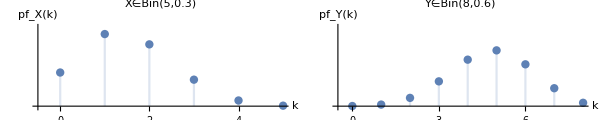

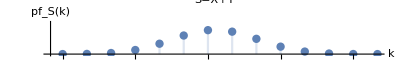

k | 0 | 1 | 2 | 3 | 4 | 5
pf_X(k) | 0.168 | 0.360 | 0.309 | 0.132 | 0.028 | 0.002
k | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
pf_Y(k) | 0.001 | 0.008 | 0.041 | 0.124 | 0.232 | 0.279 | 0.209 | 0.090 | 0.017
k | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
pf_S(k) | 1.1×10^-4 | 1.6×10^-3 | 0.010 | 0.038 | 0.097 | 0.174 | 0.225 | 0.211 | 0.143 | 0.070 | 0.024 | 5.3×10^-3 | 6.9×10^-4 | 4.1×10^-5

If we would like to continue with V=X+Y+Z  we can consider V=S+Z and use the convolution sum for S+Z.

Now, assume that all rvs X_i are independent identical distributed (iid). Introduce a variable n for the number of rvs in the sum. We want to get the probability function

pf_n(s)=P(∑_(i=1)^n X_i=s)

A convenient way here is to make a recursive definition:

{pf_1(s)=f(s)
pf_n(s)=∑_i pf_1(s-i)pf_(n-1)(i)

Mathematica

```mathematica
ClearAll["`*"]
```

The convolution example above can be computed by

```mathematica
pfX[i_]=PDF[BinomialDistribution[5,0.3],i]
```

```mathematica
pfY[i_]=PDF[BinomialDistribution[8,0.6],i]
```

```mathematica
pfS[s_]:=pfS[s]=Sum[pfX[i]pfY[s-i],{i,0,13}]
```

```mathematica
Table[pfS[s],{s,0,13}]
```

Notice the syntax

f[n_] := f[n] = methodbody

which is used to to store results in a look-up table so that a certain call only needs computation once.

See Functions That Remember Values They Have Found

There are also built-in ways of solving this, e.g. DiscreteConvolve or TransformedDistribution. Here’s an example with infinite sample space

```mathematica
Clear[pfX,pfY,pfS];
pfX[k_]=PDF[GeometricDistribution[1/3],k]
```

```mathematica
Table[pfX[k],{k,0,5}]
```

```mathematica
pfY[k_]=PDF[GeometricDistribution[1/4],k];
Table[pfY[k],{k,0,5}]
```

Notice that

pf_S(0)=pf_X(0)pf_Y(0)=1/3×1/4=1/12
pf_S(1)=pf_X(1)pf_Y(0)+pf_X(0)pf_Y(1)=2/9×1/4+1/3×3/16=17/144
…

```mathematica
pfS[s_]=DiscreteConvolve[pfX[k],pfY[k],k,s]
```

```mathematica
Table[pfS[k],{k,0,15}]//N
```

```mathematica
DiscretePlot[pfS[s],{s,0,20},AxesLabel->Automatic]
```

Now, if we have a finite and reasonably large sample space, it is very convenient to use

ListConvolve[{pfX[i_min],pfX[i_min+1],…,pfX[i_max]},{pfY[j_min],…},{1,-1},0]

for the convolution of the probabilities of  S=X+Y. Notice that the lists of probabilities should be given as a sequence from i_min to i_max (even if the probabilities are 0). The result is then a list with probabilities from pfS[i_min+j_min] to pfS[i_max+j_max].

Let’s sum two variates X of section 2.2.2.1 above.

pf_X(k)=Piecewise[{{1/3, k=3}, {1/4, k=4}, {1/5, k=6}, {13/60, k=11}, {0, otherwise}}]

We want to add two variables in S=X_1+X_2 (which is not 2X). We give the probabilities as lists

```mathematica
ClearAll["`*"]
```

```mathematica
pfX1=pfX2={1/3,1/4,0,1/5,0,0,0,0,13/60};
```

The probabilities of S=X_1+X_2 from 3+3 to 11+11 are:

```mathematica
pfS=ListConvolve[pfX1,pfX2,{1,-1},0]
```

```mathematica
data=Transpose[{Range[3+3,11+11],pfS}]
```

```mathematica
ListPlot[data,PlotRange->{{0,25},All},Filling->Axis,AxesLabel->{"k","pfS(k)"}]
```

##### Section.Subsection.Subsubsection.Subsubsubsection Continuous convolution

In the continuous case the sum is exchanged for an integral.

The distribution of a sum of two independent continuous random variables (rvs) S=X+Y can be determined by the following reasoning. If the sum S=s and we have X=x then Y=s-x. Since  X and  Y are independent the probability density can be shown to be

pdf_S(s)=(pdf_X⋆pdf_Y)(s)=∫_(-∞)^∞ pdf_X(x)pdf_Y(s-x)dx

Example: let’s say both rvs are exponentially distributed with intensity λ. Then we have, since x≥0 and s-x≥0

{x≥0
s-x≥0⇔0≤x≤s

pdf_S(s)=∫_0^s λ e^(-λ x)λ e^(-λ (s-x))dx=λ^2 e^(-λ s)∫_0^s dx=λ^2 s e^(-λ s)

It’s left to the reader to show the case λ_1≠λ_2 so we can write

pdf_S(s)=Piecewise[{{λ^2 s e^(-λ s), s≥0∧λ=λ_1=λ_2}, {(λ_1 λ_2)/(λ_2-λ_1)(e^-λ_1s-e^-λ_2s), s≥0∧λ_1≠λ_2}, {0, otherwise}}]

Now, assume that all rvs X_i are iid. Introduce a variable n for the number of rvs in the sum. We want to get the cumulative distribution function

cdf_n(s)=P(∑_(i=1)^n X_i≤s)

We can make a similar recursive definition as in the discrete case.

{cdf_1(s)=F(s)
cdf_n(s)=∫_(∀x) pdf_1(s-x)cdf_(n-1)(x)dx

{pdf_1(s)=f(s)
pdf_n(s)=∫_(∀x) pdf_1(s-x)pdf_(n-1)(x)dx

Mathematica

```mathematica
ClearAll["`*"]
```

The convolution example above, with λ_1=1/5 and λ_2=1/7, can be computed by

```mathematica
λ1=1/5;
pdfX[x_]=PDF[ExponentialDistribution[λ1],x]
```

```mathematica
λ2=1/7;
pdfY[x_]=PDF[ExponentialDistribution[λ2],x]
```

```mathematica
pdfS[s_]=Integrate[pdfX[t]pdfY[s-t],{t,0,s},Assumptions->s>0]//Expand
```

```mathematica
(* compare *)
(λ1 λ2)/(λ2-λ1)(ⅇ^(-λ1 s)-ⅇ^(-λ2 s))//Expand
```

```mathematica
Plot[pdfS[s],{s,0,50},AxesLabel->Automatic]
```

There are also built-in ways of solving this, e.g. Convolve or TransformedDistribution. 
If all rvs are independent iid with exponential distribution it can be shown that the sum has ErlangDistribution[n, λ] or equivalently GammaDistribution[n, 1/λ].

#### Section.Subsection.Subsubsection Simulation

##### Section.Subsection.Subsubsection.Subsubsubsection Discrete distribution

The idea with simulation is often to compute some unknown parameters or distributions which are too complicated to calculate. However in this simple example we will do a simulation of a simple distribution which is easy to calculate. In this way we can check the validity.

Let’s pick the sum of two ordinary dice. The distribution is the convolution as above:

```mathematica
ClearAll["`*"]
```

```mathematica
pf1=ConstantArray[1,6]/6
```

```mathematica
pf2=pf1;
```

```mathematica
pfS=ListConvolve[pf1,pf2,{1,-1},0]
```

```mathematica
ListPlot[{Range[2,12],pfS}//Transpose,AxesLabel->{"s","pf(s)"}]
```

An easy way to make a simulation here is to create random integers and add them.

```mathematica
d1:=RandomInteger[{1,6}];
d2:=RandomInteger[{1,6}];
s:=d1+d2
```

```mathematica
n=100;
data=Table[s,{n}]
```

```mathematica
frequencies=Tally[data]
```

```mathematica
ListPlot[frequencies,Filling->Axis,PlotLabel->"frequencies"]
```

If we divide by the number of trials we get the relative frequency which is an estimate of the probabilities.

```mathematica
{𝕤,𝔽}=Transpose[frequencies]
```

```mathematica
𝕗=𝔽/n
```

```mathematica
ListPlot[Transpose[{𝕤,𝕗}],Filling->Axis,PlotLabel->"relative frequencies"]
```

A good principle in simulation is to minimize the number of method calls, i.e. use

rnd[nLarge] instead of Table[rnd[1],{nLarge}]

Let’s increase the sample size to 10^4.

```mathematica
n=10^4;
d1=RandomInteger[{1,6},n];
d2=RandomInteger[{1,6},n];
s=d1+d2;
frequencies=Tally[s]
```

```mathematica
{𝕤,𝔽}=Transpose[frequencies];
𝕗=N[𝔽/n]
```

```mathematica
ListPlot[Transpose[{𝕤,𝕗}],Filling->Axis,PlotLabel->"relative frequencies"]
```

A more general approach is to use RandomVariate which works for different distributions.

```mathematica
𝒟=DiscreteUniformDistribution[{1,6}];
```

```mathematica
n=10^4;
d1=RandomVariate[𝒟,n];
d2=RandomInteger[𝒟,n];
s=d1+d2;
frequencies=Tally[s]
```

```mathematica
ListPlot[frequencies,Filling->Axis,PlotLabel->"frequencies"]
```

Now, if we want to estimate the probability of a certain event we can create a method that returns a Boole value and the simply count the relative frequency. Here’s a simple example

```mathematica
event0[sum_]:=sum≥8
```

```mathematica
{event0[5],event0[11]}
```

```mathematica
event[sum_]:=Boole[sum≥8]
```

```mathematica
{event[5],event[11]}
```

Now, call the event method for a large number of trials, compute the sum (of all 1:s) and divide by the number of trials. Then, we have a probability estimate for the event.

```mathematica
n=100;
d1=RandomVariate[𝒟,n];
d2=RandomInteger[𝒟,n];
s=d1+d2
```

```mathematica
event/@s
```

```mathematica
probEstimate=Total[event/@s]/n
```

We will get a better estimate if we increase the sample size. We will give a quality measure later in the course.

```mathematica
n=10^4;
d1=RandomVariate[𝒟,n];
d2=RandomInteger[𝒟,n];
s=d1+d2;
N[probEstimate=Total[event/@s]/n]
```

##### Section.Subsection.Subsubsection.Subsubsubsection Continuous distribution

Let’s say we want to simulate the life time of simple light bulbs with average life time 8 years. We assume that the life time is exponential distributed.

In one room there are 8 light bulbs. We want to replace all the bulbs when the probability that at least five lights are less than 90%.

We start by the simulation of some life times.

```mathematica
ClearAll["`*"]
```

```mathematica
λ=1/8;
𝒟=ExponentialDistribution[λ];
```

```mathematica
n=10;
t=RandomVariate[𝒟,n]
```

The simulation of 8 light bulbs per sample is done as a matrix.

```mathematica
n=10;
lifeTimes=RandomVariate[𝒟,{n,8}]
```

Let’s pick the first sample and check whether five lights at the time 2 years.

```mathematica
lifeTimes⟦1⟧
```

```mathematica
Thread[lifeTimes⟦1⟧>2]
```

How many lights?

```mathematica
Total[Boole[Thread[lifeTimes⟦1⟧>2]]]
```

Five or more?

```mathematica
Total[Boole[Thread[lifeTimes⟦1⟧>2]]]≥5
```

Let’s make a query method for this.

```mathematica
fiveLightsQ[t_][sample_]:=Total[Boole[Thread[sample>t]]]≥5
```

Check all 10 samples:

```mathematica
fiveLightsQ[2]/@lifeTimes
```

A probability estimate:

```mathematica
Total[Boole[fiveLightsQ[2]/@lifeTimes]]/n
```

We increase the number of samples and get a better estimate.

```mathematica
n=10^4;
lifeTimes=RandomVariate[𝒟,{n,8}];
```

```mathematica
probData=Table[{t,Total[Boole[fiveLightsQ[t]/@lifeTimes]]/n},{t,0.25,10,0.25}]//N
```

```mathematica
ListLinePlot[probData,AxesLabel->{"replace time [yr]", "five lights probability"}]
```

The probData can be interpolated to a function by

```mathematica
fiveLightsProb=Interpolation[probData]
```

We look for the the time when the estimated probability is 90%.

```mathematica
t90=t/.FindRoot[fiveLightsProb[t]==0.9,{t,2}]
```

We ought to replace the bulbs every 2.2 year or every 26^th month.

Also in this case it is possible to calculate the desired time directly from the distribution. The probability of light at the time t is

P(𝔱>t)=1-cdf(t)=1-(1-e^(-λ t))=e^(-λ t)

```mathematica
pLight[t_]=Simplify[1-CDF[𝒟,t],t≥0]
```

The number of lights 𝔑∈Bin(8,e^(-t/8)) so

```mathematica
𝒟5[t_]:=BinomialDistribution[8,ⅇ^(-t/8)];
(* five or more *)
p5lights[t_]:=1-CDF[𝒟5[t],4]
```

We search for the time when the probability is 90% that we have five lights (or more).

```mathematica
t90=t/.FindRoot[p5lights[t]==0.9,{t,2}]
```

```mathematica
Plot[p5lights[t],{t,0,10},AxesLabel->{"replace time [yr]", "five lights probability"}]
```

#### Section.Subsection.Subsubsection Approximation with Normal Distribution

##### Section.Subsection.Subsubsection.Subsubsubsection Discrete distribution

The principle is the following. For a discrete distribution the pf is often illustrated in a bar-chart or similar where the probabilities are the heights of the bars, example

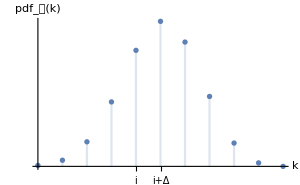

When you approximate with normal distribution you use the parameters μ and σ of you discrete distribution or your data as estimates. The height of a bar in the discrete distribution, pf_𝒟(k) becomes the area below the normal pdf_𝒩(x) curve, i.e.

pf_𝒟(i)≈∫_(i-Δ/2)^(i+Δ/2) pdf_𝒩(x)dx

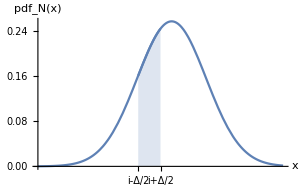

This means that if you have a data sample, compute

μ = Mean[data];
σ = StandardDeviation[data];

and use the following distribution

𝒟 = NormalDistribution[μ, σ]

Notice that pf_𝒟(i)≈cdf_𝒩(i+Δ)-cdf_𝒩(i-Δ) and cdf_𝒟(i)≈cdf_𝒩(i+Δ).

##### Section.Subsection.Subsubsection.Subsubsubsection Continuous distribution

For a continuous distribution the computation is straight forward.

pdf_𝒟(x)≈pdf_𝒩(x), cdf_𝒟(x)≈cdf_𝒩(x)

with the parameter estimations (μ,σ) as in the discrete case.

## Section. Mathematical Task

Basic task is required for grade E (approved). Advanced task is required if you aim at higher grade. Keep in mind that it is the mathematical method on the task that is interesting to consider, not the answer. Furthermore, solve the given task, not a variant or extension.

Read Section 2.2 Guidance very carefully before delving into the mathematical tasks!

A general hint is to start in a small scale and test your methods with not too large numbers.

It is better to take advantage of that you are using a mathematical programming language. You don’t need to “re-invent the wheel”.

### Basic task: Winning a teddy

In the discrete math course you learned how to do a census by computing all possibilities and use the classical definition of probability. In the following problems you are expected to use convolution.

-Graphics-

At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up.

At a fun-fair stall you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact (no floating point, please) probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

### Advanced task: Normal distribution

Since we have the exact probabilities we can compare with the approximate answer given by the normal distribution.

Determine the expectation value and standard deviation of the distribution in the Teddy case.

Determine the probability of the Teddy prize using the normal distribution.

Compare and comment on the results.